## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
```

```mathematica
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

```mathematica
SetDirectory[basepath<>"/output"];
```

```mathematica
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
```

```mathematica
Needs["LatticeAnalysis`"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
<<"LatticeAnalysis`"
```

```mathematica
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

```mathematica
numsamples=All; (*number of samples to take for error estimates. Set to "All" if not in debug-mode!*)
```

The following line sets up blocking during the creation of Jackknife samples with block size 1.

```mathematica
MakeJacknifeSamplesB[x_]:=MakeJacknifeSamples[x,1];
```

```mathematica
thisquarkchannel="down";
```

## Constants

```mathematica
scalingNat = .1973270524; (* this is GeV*fm *)
```

```mathematica
quarkchannelshort[quarkchannel_]:=Switch[quarkchannel,"up","U","down","D","u-d","UminusD",_,Message["INVALID QUARK CHANNEL"]];
```

```mathematica
basedatapath="/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_x/"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_x/

```mathematica
exportdatapath[quarkchannel_]:=basedatapath<>quarkchannelshort[quarkchannel]<>"_";
```

```mathematica
resamplingext="_"<>"jn";
```

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
platdb1=BIDATEXReader[exportdatapath[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
```

< -MemDB- {correlatorType,gammaValue,linkPath,momTransfer,numberFilter,section,seqPropNum,sideExtent,sideLink,sideNum,sinkMom,sourceType,tSep,tSink,tSource,analysisStep,data}>

Now, let’s reproduce preliminary plots from Dr. Engelhardt’s talk
We have,

for making even and odd in  , we need  and corresponding  which satisfy the constraint above.

```mathematica
PlotbLbT[sideNumForPlusvT_, sideNumForMinusvT_]:=Module[
{PlotbLfull,PlotbL, Plotfit, PlotfitbLbT, Cast, xFourier},
Print["quark -> ",thisquarkchannel];
Print["Given sideNum ", sideNumForPlusvT, " & ", sideNumForMinusvT, "."];
LinkPathListForPlusvT = MemDBGet[platdb1,MemDBSelect[platdb1,{sideNum-> sideNumForPlusvT}],linkPath];
DistinctLinkPathsForPlusvT= DeleteDuplicates[LinkPathListForPlusvT];
VectorDistinctLinkPathsForPlusvT = Array[PathToShift[DistinctLinkPathsForPlusvT[[#]],3]&,CountDistinct[LinkPathListForPlusvT]];
bTableVectorPathForPlusvT=Table[{VectorDistinctLinkPathsForPlusvT[[i]],DistinctLinkPathsForPlusvT[[i]]},{i,Length[DistinctLinkPathsForPlusvT]}];
(*Do[Print[i,") ",bTableVectorPathForPlusvT[[i,1]],"<------->",bTableVectorPathForPlusvT[[i,2]]],{i,CountDistinct[LinkPathListForPlusvT]}]*)
LinkPathListForMinusvT = MemDBGet[platdb1,MemDBSelect[platdb1,{sideNum-> sideNumForMinusvT}],linkPath];
DistinctLinkPathsForMinusvT= DeleteDuplicates[LinkPathListForMinusvT];
VectorDistinctLinkPathsForMinusvT = Array[PathToShift[DistinctLinkPathsForMinusvT[[#]],3]&,CountDistinct[LinkPathListForMinusvT]];
bTableVectorPathForMinusvT=Table[{VectorDistinctLinkPathsForMinusvT[[i]],DistinctLinkPathsForMinusvT[[i]]},{i,Length[DistinctLinkPathsForMinusvT]}];
(*Do[Print[i,") ",bTableVectorPathForMinusvT[[i,1]],"<------->",bTableVectorPathForMinusvT[[i,2]]],{i,CountDistinct[LinkPathListForMinusvT]}]*)
(*check b1*)
noError=True;
Do[If[(bTableVectorPathForPlusvT[[i,1]][[1]]+bTableVectorPathForMinusvT[[i,1]][[1]])=!=0,Print["Mismatch in finding   at bTableVectorPathForMinusvT[",i, "]"];noError=False;],{i,Length[DistinctLinkPathsForMinusvT]}];
If[noError,Print["✓ Checked: linkPaths corresponding to   are found for given sideNum ", sideNumForPlusvT, " & ", sideNumForMinusvT]];
noErrorvT=True;
(*check v1*)
Do[
Do[If[((PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bTableVectorPathForPlusvT[[i,2]],sideNum-> sideNumForPlusvT,numberFilter->Re}],sideLink][[num]],3][[2]])+(PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bTableVectorPathForMinusvT[[i,2]],sideNum-> sideNumForMinusvT,numberFilter->Re}],sideLink][[num]],3][[2]]))=!=0,Print["Mismatch in finding   at bTableVectorPathForMinusvT[",i, "]"];noErrorvT=False;]
,{num,Length[Union[MemDBGet[platdb1,MemDBSelect[platdb1,{sideNum-> sideNumForPlusvT}],sideExtent]]]}]
,{i,Length[DistinctLinkPathsForMinusvT]}];
If[noErrorvT,Print["✓ Checked: sideLink corresponding to sideNum ", sideNumForPlusvT, " & ", sideNumForMinusvT, " are   for given  "]];
Print["✓ Checked:  , constraint satisfied!"];
TablePlateauEvengPlusImForb = {};
TablePlateaugPlusImForb = {};
Do[
blPg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bTableVectorPathForPlusvT[[i,2]],sideNum-> sideNumForPlusvT,numberFilter->Im}],{sideExtent,data}];
blPg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bTableVectorPathForPlusvT[[i,2]],sideNum-> sideNumForPlusvT,numberFilter->Re}],{sideExtent,data}];
blNg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bTableVectorPathForMinusvT[[i,2]],sideNum-> sideNumForMinusvT,numberFilter->Im}],{sideExtent,data}];
blNg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bTableVectorPathForMinusvT[[i,2]],sideNum-> sideNumForMinusvT,numberFilter->Re}],{sideExtent,data}];
etaList = blPg8Im[[All,1]];
blPgPlusIm = (blPg1Re[[All, 2]]+blPg8Im[[All, 2]])/Sqrt[2];
blNgPlusIm = (blNg1Re[[All, 2]]+blNg8Im[[All, 2]])/Sqrt[2];
blEvengPlusIm = (blPgPlusIm+blNgPlusIm)/2;
PlotblEvengPlusIm=Transpose[{etaList,blEvengPlusIm}];
PlotblPgPlusIm=Transpose[{etaList,blPgPlusIm}];
PlotblNgPlusIm=Transpose[{etaList,blNgPlusIm}];
(*plot3 = ErrorListPlot[MakeErrBars[PlotblEvengPlusIm],FrameLabel->{Style[η,Large],Style[,Large]}, Frame->True];*)
PlateauRange=Table[(Round[((Length[etaList]-1)/2)]-5+n),{n,0,4}];
     PlateauPluseta = 0;
PlateauMinuseta = 0;
PlateauPlusetablP = 0;
PlateauMinusetablP = 0;
PlateauPlusetablN = 0;
PlateauMinusetablN = 0;
Do[
blEvengPlusImEta=Select[PlotblEvengPlusIm,#[[1]]==PlateauEta&][[All,2]];
blEvengMinusImEta=Select[PlotblEvengPlusIm,#[[1]]==-PlateauEta&][[All,2]];

blPgPlusImEta=Select[PlotblPgPlusIm,#[[1]]==PlateauEta&][[All,2]];
blPgMinusImEta=Select[PlotblPgPlusIm,#[[1]]==-PlateauEta&][[All,2]];

blNgPlusImEta=Select[PlotblNgPlusIm,#[[1]]==PlateauEta&][[All,2]];
blNgMinusImEta=Select[PlotblNgPlusIm,#[[1]]==-PlateauEta&][[All,2]];

PlateauPluseta+=blEvengPlusImEta/Length[PlateauRange];
PlateauMinuseta+=blEvengMinusImEta/Length[PlateauRange];

PlateauPlusetablP+=blPgPlusImEta/Length[PlateauRange];
PlateauMinusetablP+=blPgMinusImEta/Length[PlateauRange];

PlateauPlusetablN+=blNgPlusImEta/Length[PlateauRange];
PlateauMinusetablN+=blNgMinusImEta/Length[PlateauRange];
,{PlateauEta, PlateauRange}];
PlateauEvengPlusIm = (-PlateauMinuseta+PlateauPluseta)/2;
(*PlateaublPgPlusIm = (-PlateauMinusetablP+PlateauPlusetablP)/2;
PlateaublNgPlusIm = (-PlateauMinusetablN+PlateauPlusetablN)/2;*)
PlateaublPgPlusIm = (-PlateauMinusetablP);
PlateaublNgPlusIm = (-PlateauMinusetablN);
AppendTo[TablePlateauEvengPlusImForb,{bTableVectorPathForPlusvT[[i,1]],PlateauEvengPlusIm[[1]]}];
AppendTo[TablePlateauEvengPlusImForb,{bTableVectorPathForMinusvT[[i,1]],PlateauEvengPlusIm[[1]]}];

AppendTo[TablePlateaugPlusImForb,{bTableVectorPathForPlusvT[[i,1]],PlateaublPgPlusIm[[1]]}];
AppendTo[TablePlateaugPlusImForb,{bTableVectorPathForMinusvT[[i,1]],PlateaublNgPlusIm[[1]]}];
  ,{i,Length[DistinctLinkPathsForMinusvT]}];
Print["Averaging  values: ",PlateauRange];
groupSamebFullgPlusImg=GroupBy[TablePlateaugPlusImForb,First->Last];
averagedTablePlateaugPlusImForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebFullgPlusImg];
Print["✓ Same  with different linkPath are averaged\n"];
Print["               Imaginary part of  correlator"];
bTlistFullgPlusImg= Union[averagedTablePlateaugPlusImForb[[All,1]][[All,2]]];
bLlistFullgPlusImg= Union[averagedTablePlateaugPlusImForb[[All,1]][[All,1]]];
PlotbLforDiffbTListforFullgPlusImg={};
Do[
PlotbL1=Transpose[{Select[averagedTablePlateaugPlusImForb, #[[1,2]]==bTlistFullgPlusImg[[bT]]&][[All,1]][[All,1]],Select[averagedTablePlateaugPlusImForb, #[[1,2]]==bTlistFullgPlusImg[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTListforFullgPlusImg,PlotbL1];
 ,{bT,bTlistFullgPlusImg}];
PlotbLfull= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTListforFullgPlusImg[[bT]]],{bT, Length[bTlistFullgPlusImg]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlistFullgPlusImg[[bT]]],{bT,Length[bTlistFullgPlusImg]}]];
Print[PlotbLfull];
groupSameb=GroupBy[TablePlateauEvengPlusImForb,First->Last];
averagedTablePlateauEvengPlusImForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
Print["✓ Same  with different linkPath are averaged\n"];
Print["     -even component of imaginary part of  correlator"];
bTlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,2]]];
bLlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,1]]];
PlotbLforDiffbTList={};
Do[
PlotbL2=Transpose[{Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTList,PlotbL2];
 ,{bT,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Print[PlotbL];
datafor2dGaussianFitbLbTerrors={};
Do[
dataPointErr=MakeErrBars[PlotbLforDiffbTList[[TagbT]]];
Do[
AppendTo[datafor2dGaussianFitbLbTerrors,{{dataPointErr[[All,1]][[TagbL]][[1]],bTlist[[TagbT]],dataPointErr[[All,1]][[TagbL]][[2]]},dataPointErr[[All,2,1]][[TagbL]]}];
,{TagbL,Length[dataPointErr]}];
,{TagbT,Length[bTlist]}];
points=datafor2dGaussianFitbLbTerrors[[All,1]];
errors=datafor2dGaussianFitbLbTerrors[[All,2]];
fitbLbLbT=NonlinearModelFit[points,A*Exp[-((alpha*()^2)+(beta*()^2))],{A,alpha, beta},{,},Weights->1/(errors[[All,2]]^2),Method->"LevenbergMarquardt",MaxIterations->10000];
Print["Fitting into   = ",Normal[fitbLbLbT]];
Print["\n             Fit dependence in  space"];
PlotfitbLbT=Show[PlotbL,Table[Plot[fitbLbLbT[x,bT],{x,Min[bLlist],Max[bLlist]},PlotStyle->ColorData[97,"ColorList"][[bT]]],{bT,1,Length[bTlist]}]];
Print[PlotfitbLbT];
Print["\n                 Cast in ,  space"];
FnbdotPbsqre[bp_,b2_]:=(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))];
bsquarelist={1,4,9,16};
PlotbLdata= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Cast=Show[PlotbLdata,Table[Plot[FnbdotPbsqre[x,bsq],{x,Min[bLlist],Max[bLlist]}, Frame->True],{bsq,bsquarelist}]];
Print[Cast];
Print[" = ",bsquarelist];
Print["\n                 Fourier transform "];
xFourierTransf[x_, b2_]:= FourierTransform[(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))],bp,x];
xFourier=Show[Table[Plot[xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
Print["\n    Normalize to -integrated Sivers shift, multiply by "];
xFourier=Show[Table[Plot[-x*xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
]

PlotbLbTwith2Pi[sideNumForPlusvT_, sideNumForMinusvT_]:=Module[
{PlotbLfull,PlotbL, Plotfit, PlotfitbLbT, Cast, xFourier},
Print["quark -> ",thisquarkchannel];
Print["Given sideNum ", sideNumForPlusvT, " & ", sideNumForMinusvT, "."];
LinkPathListForPlusvT = MemDBGet[platdb1,MemDBSelect[platdb1,{sideNum-> sideNumForPlusvT}],linkPath];
DistinctLinkPathsForPlusvT= DeleteDuplicates[LinkPathListForPlusvT];
VectorDistinctLinkPathsForPlusvT = Array[PathToShift[DistinctLinkPathsForPlusvT[[#]],3]&,CountDistinct[LinkPathListForPlusvT]];
bTableVectorPathForPlusvT=Table[{VectorDistinctLinkPathsForPlusvT[[i]],DistinctLinkPathsForPlusvT[[i]]},{i,Length[DistinctLinkPathsForPlusvT]}];
(*Do[Print[i,") ",bTableVectorPathForPlusvT[[i,1]],"<------->",bTableVectorPathForPlusvT[[i,2]]],{i,CountDistinct[LinkPathListForPlusvT]}]*)
LinkPathListForMinusvT = MemDBGet[platdb1,MemDBSelect[platdb1,{sideNum-> sideNumForMinusvT}],linkPath];
DistinctLinkPathsForMinusvT= DeleteDuplicates[LinkPathListForMinusvT];
VectorDistinctLinkPathsForMinusvT = Array[PathToShift[DistinctLinkPathsForMinusvT[[#]],3]&,CountDistinct[LinkPathListForMinusvT]];
bTableVectorPathForMinusvT=Table[{VectorDistinctLinkPathsForMinusvT[[i]],DistinctLinkPathsForMinusvT[[i]]},{i,Length[DistinctLinkPathsForMinusvT]}];
(*Do[Print[i,") ",bTableVectorPathForMinusvT[[i,1]],"<------->",bTableVectorPathForMinusvT[[i,2]]],{i,CountDistinct[LinkPathListForMinusvT]}]*)
(*check b1*)
noError=True;
Do[If[(bTableVectorPathForPlusvT[[i,1]][[1]]+bTableVectorPathForMinusvT[[i,1]][[1]])=!=0,Print["Mismatch in finding   at bTableVectorPathForMinusvT[",i, "]"];noError=False;],{i,Length[DistinctLinkPathsForMinusvT]}];
If[noError,Print["✓ Checked: linkPaths corresponding to   are found for given sideNum ", sideNumForPlusvT, " & ", sideNumForMinusvT]];
noErrorvT=True;
(*check v1*)
Do[
Do[If[((PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bTableVectorPathForPlusvT[[i,2]],sideNum-> sideNumForPlusvT,numberFilter->Re}],sideLink][[num]],3][[2]])+(PathToShift[MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->bTableVectorPathForMinusvT[[i,2]],sideNum-> sideNumForMinusvT,numberFilter->Re}],sideLink][[num]],3][[2]]))=!=0,Print["Mismatch in finding   at bTableVectorPathForMinusvT[",i, "]"];noErrorvT=False;]
,{num,Length[Union[MemDBGet[platdb1,MemDBSelect[platdb1,{sideNum-> sideNumForPlusvT}],sideExtent]]]}]
,{i,Length[DistinctLinkPathsForMinusvT]}];
If[noErrorvT,Print["✓ Checked: sideLink corresponding to sideNum ", sideNumForPlusvT, " & ", sideNumForMinusvT, " are   for given  "]];
Print["✓ Checked:  , constraint satisfied!"];
TablePlateauEvengPlusImForb = {};
TablePlateaugPlusImForb = {};
Do[
blPg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bTableVectorPathForPlusvT[[i,2]],sideNum-> sideNumForPlusvT,numberFilter->Im}],{sideExtent,data}];
blPg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bTableVectorPathForPlusvT[[i,2]],sideNum-> sideNumForPlusvT,numberFilter->Re}],{sideExtent,data}];
blNg8Im = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,linkPath->bTableVectorPathForMinusvT[[i,2]],sideNum-> sideNumForMinusvT,numberFilter->Im}],{sideExtent,data}];
blNg1Re = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->1,linkPath->bTableVectorPathForMinusvT[[i,2]],sideNum-> sideNumForMinusvT,numberFilter->Re}],{sideExtent,data}];
etaList = blPg8Im[[All,1]];
blPgPlusIm = (blPg1Re[[All, 2]]+blPg8Im[[All, 2]])/Sqrt[2];
blNgPlusIm = (blNg1Re[[All, 2]]+blNg8Im[[All, 2]])/Sqrt[2];
blEvengPlusIm = (blPgPlusIm+blNgPlusIm)/2;
PlotblEvengPlusIm=Transpose[{etaList,blEvengPlusIm}];
PlotblPgPlusIm=Transpose[{etaList,blPgPlusIm}];
PlotblNgPlusIm=Transpose[{etaList,blNgPlusIm}];
(*plot3 = ErrorListPlot[MakeErrBars[PlotblEvengPlusIm],FrameLabel->{Style[η,Large],Style[,Large]}, Frame->True];*)
PlateauRange=Table[(Round[((Length[etaList]-1)/2)]-5+n),{n,0,4}];
     PlateauPluseta = 0;
PlateauMinuseta = 0;
PlateauPlusetablP = 0;
PlateauMinusetablP = 0;
PlateauPlusetablN = 0;
PlateauMinusetablN = 0;
Do[
blEvengPlusImEta=Select[PlotblEvengPlusIm,#[[1]]==PlateauEta&][[All,2]];
blEvengMinusImEta=Select[PlotblEvengPlusIm,#[[1]]==-PlateauEta&][[All,2]];

blPgPlusImEta=Select[PlotblPgPlusIm,#[[1]]==PlateauEta&][[All,2]];
blPgMinusImEta=Select[PlotblPgPlusIm,#[[1]]==-PlateauEta&][[All,2]];

blNgPlusImEta=Select[PlotblNgPlusIm,#[[1]]==PlateauEta&][[All,2]];
blNgMinusImEta=Select[PlotblNgPlusIm,#[[1]]==-PlateauEta&][[All,2]];

PlateauPluseta+=blEvengPlusImEta/Length[PlateauRange];
PlateauMinuseta+=blEvengMinusImEta/Length[PlateauRange];

PlateauPlusetablP+=blPgPlusImEta/Length[PlateauRange];
PlateauMinusetablP+=blPgMinusImEta/Length[PlateauRange];

PlateauPlusetablN+=blNgPlusImEta/Length[PlateauRange];
PlateauMinusetablN+=blNgMinusImEta/Length[PlateauRange];
,{PlateauEta, PlateauRange}];
PlateauEvengPlusIm = (-PlateauMinuseta+PlateauPluseta)/2;
(*PlateaublPgPlusIm = (-PlateauMinusetablP+PlateauPlusetablP)/2;
PlateaublNgPlusIm = (-PlateauMinusetablN+PlateauPlusetablN)/2;*)
PlateaublPgPlusIm = (-PlateauMinusetablP);
PlateaublNgPlusIm = (-PlateauMinusetablN);
AppendTo[TablePlateauEvengPlusImForb,{bTableVectorPathForPlusvT[[i,1]],PlateauEvengPlusIm[[1]]}];
AppendTo[TablePlateauEvengPlusImForb,{bTableVectorPathForMinusvT[[i,1]],PlateauEvengPlusIm[[1]]}];

AppendTo[TablePlateaugPlusImForb,{bTableVectorPathForPlusvT[[i,1]],PlateaublPgPlusIm[[1]]}];
AppendTo[TablePlateaugPlusImForb,{bTableVectorPathForMinusvT[[i,1]],PlateaublNgPlusIm[[1]]}];
  ,{i,Length[DistinctLinkPathsForMinusvT]}];
Print["Averaging  values: ",PlateauRange];
groupSamebFullgPlusImg=GroupBy[TablePlateaugPlusImForb,First->Last];
averagedTablePlateaugPlusImForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebFullgPlusImg];
Print["✓ Same  with different linkPath are averaged\n"];
Print["               Imaginary part of  correlator"];
bTlistFullgPlusImg= Union[averagedTablePlateaugPlusImForb[[All,1]][[All,2]]];
bLlistFullgPlusImg= Union[averagedTablePlateaugPlusImForb[[All,1]][[All,1]]];
PlotbLforDiffbTListforFullgPlusImg={};
Do[
PlotbL1=Transpose[{Select[averagedTablePlateaugPlusImForb, #[[1,2]]==bTlistFullgPlusImg[[bT]]&][[All,1]][[All,1]],Select[averagedTablePlateaugPlusImForb, #[[1,2]]==bTlistFullgPlusImg[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTListforFullgPlusImg,PlotbL1];
 ,{bT,bTlistFullgPlusImg}];
PlotbLfull= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTListforFullgPlusImg[[bT]]],{bT, Length[bTlistFullgPlusImg]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlistFullgPlusImg[[bT]]],{bT,Length[bTlistFullgPlusImg]}]];
Print[PlotbLfull];
groupSameb=GroupBy[TablePlateauEvengPlusImForb,First->Last];
averagedTablePlateauEvengPlusImForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
Print["✓ Same  with different linkPath are averaged\n"];
Print["     -even component of imaginary part of  correlator"];
bTlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,2]]];
bLlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,1]]];
PlotbLforDiffbTList={};
Do[
PlotbL2=Transpose[{Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTList,PlotbL2];
 ,{bT,bTlist}];
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Print[PlotbL];
datafor2dGaussianFitbLbTerrors={};
Do[
dataPointErr=MakeErrBars[PlotbLforDiffbTList[[TagbT]]];
Do[
AppendTo[datafor2dGaussianFitbLbTerrors,{{dataPointErr[[All,1]][[TagbL]][[1]],bTlist[[TagbT]],dataPointErr[[All,1]][[TagbL]][[2]]},dataPointErr[[All,2,1]][[TagbL]]}];
,{TagbL,Length[dataPointErr]}];
,{TagbT,Length[bTlist]}];
points=datafor2dGaussianFitbLbTerrors[[All,1]];
errors=datafor2dGaussianFitbLbTerrors[[All,2]];
fitbLbLbT=NonlinearModelFit[points,A*Exp[-((alpha*()^2)+(beta*()^2))],{A,alpha, beta},{,},Weights->1/(errors[[All,2]]^2),Method->"LevenbergMarquardt",MaxIterations->10000];
Print["Fitting into   = ",Normal[fitbLbLbT]];
Print["\n             Fit dependence in  space"];
PlotfitbLbT=Show[PlotbL,Table[Plot[fitbLbLbT[x,bT],{x,Min[bLlist],Max[bLlist]},PlotStyle->ColorData[97,"ColorList"][[bT]]],{bT,1,Length[bTlist]}]];
Print[PlotfitbLbT];
Print["\n                 Cast in ,  space"];
FnbdotPbsqre[bp_,b2_]:=(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*((32/(2N[Pi]))^2*alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))];
bsquarelist={1,4,9,16};
PlotbLdata= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Cast=Show[PlotbLdata,Table[Plot[FnbdotPbsqre[x,bsq],{x,Min[bLlist],Max[bLlist]}, Frame->True],{bsq,bsquarelist}]];
Print[Cast];
Print[" = ",bsquarelist];
Print["\n                 Fourier transform "];
xFourierTransf[x_, b2_]:= FourierTransform[(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*((32/(2N[Pi]))^2*alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))],bp,x];
xFourier=Show[Table[Plot[xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
Print["\n    Normalize to -integrated Sivers shift, multiply by "];
xFourier=Show[Table[Plot[-x*xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
]
```

quark -> down

Given sideNum 18 & 23.

✓ Checked: linkPaths corresponding to   are found for given sideNum 18 & 23

✓ Checked: sideLink corresponding to sideNum 18 & 23 are   for given

✓ Checked:  , constraint satisfied!

Averaging  values: {12,13,14,15,16}

✓ Same  with different linkPath are averaged

Imaginary part of  correlator

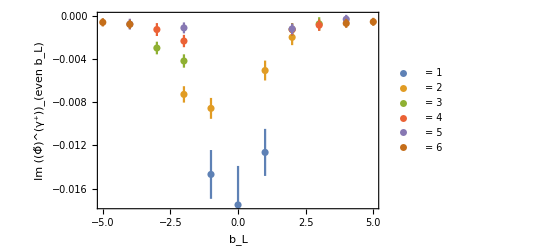

✓ Same  with different linkPath are averaged

-even component of imaginary part of  correlator

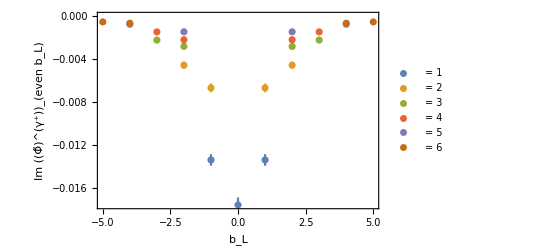

Fitting into   = -0.014854 ⅇ^(-0.153631 b_L^2-0.0965616 b_T^2)

Fit dependence in  space

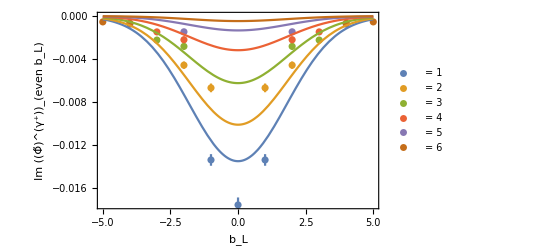

Cast in ,  space

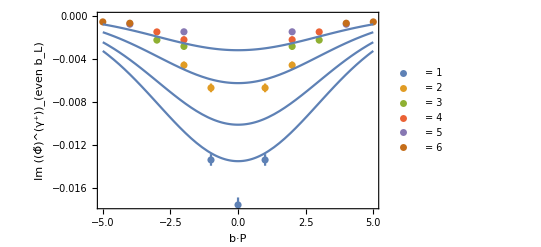

= {1,4,9,16}

Fourier transform

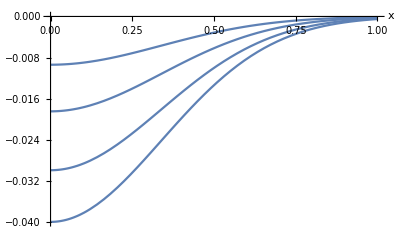

Normalize to -integrated Sivers shift, multiply by

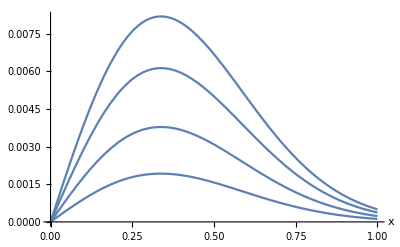

```mathematica
PlotbLbT[sideNumForPlusvT = 18, sideNumForMinusvT = 23]
```

quark -> down

Given sideNum 18 & 23.

✓ Checked: linkPaths corresponding to   are found for given sideNum 18 & 23

✓ Checked: sideLink corresponding to sideNum 18 & 23 are   for given

✓ Checked:  , constraint satisfied!

Averaging  values: {12,13,14,15,16}

✓ Same  with different linkPath are averaged

Imaginary part of  correlator

-Graphics-

✓ Same  with different linkPath are averaged

-even component of imaginary part of  correlator

-Graphics-

Fitting into   = -0.014854 ⅇ^(-0.153631 b_L^2-0.0965616 b_T^2)

Fit dependence in  space

-Graphics-

Cast in ,  space

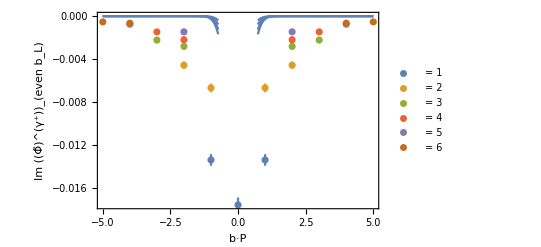

= {1,4,9,16}

Fourier transform

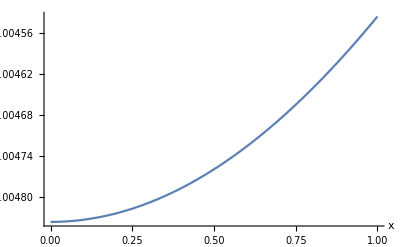

Normalize to -integrated Sivers shift, multiply by

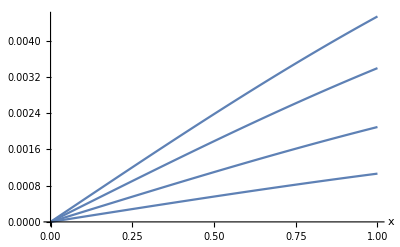

```mathematica
PlotbLbTwith2Pi[sideNumForPlusvT = 18, sideNumForMinusvT = 23]
```